# Demo

```mathematica
SetDirectory[NotebookDirectory[]];
skmfile="Data/skel-w-msure-data/323-5_t35_proc_ma_skel.skMsure";
```

```mathematica
Needs["CornRootsFileReader`","Packages/CornRootsFileReader.wl"]
Needs["VisualizationFunctions`","Packages/VisualizationFunctions.wl"]
Needs["OperationFunctions`","Packages/OperationFunctions.wl"]
```

```mathematica
{vertices, edges, faces,edgeMeasure,faceMeasure}=ParseSKMfile[skmfile];
{thickness,width,length}=Transpose@edgeMeasure;
```

### Graph3DLength

```mathematica
Graph3DLength[vertices,edges,length]
```

-Graphics3D-

### Task 1: Extract Infinite Length Part

```mathematica
loopGraphics=ExtractInfinitePart[vertices,edges,length,Blue]
```

-Graphics3D-

### Task 2: Manipulate

```mathematica
loopEdges=ExtractInfiniteEdges[vertices, edges, length];
```

```mathematica
limitedVertices=vertices⟦#⟧&/@Union[Flatten[loopEdges]];
minMaxOfVertices = MinMax/@Transpose[limitedVertices];
boundingBox=RescalingParameter[minMaxOfVertices]
```

{{175,230.667},{98.474,173.25},{35,190.167}}

```mathematica
Manipulate[
{id1 ,id2}=loopEdges⟦i⟧;
p1=vertices⟦id1⟧;
p2=vertices⟦id2⟧;
midPt=(p1+p2)/2;

Show[loopGraphics,Graphics3D[{Text[Style[i,Medium],midPt],Thick,Red,GraphicsComplex[vertices,Line[loopEdges⟦i⟧]],Box->False}],PlotRange->boundingBox],{i,1,Length[loopEdges]-1,1}]
```

### Task 3: Implement Graph Operations

```mathematica
graphData=MapThread[#1<->#2&,Transpose@loopEdges];
```

```mathematica
vertexDegree3Pos=FindVertexDegree3Position[graphData]
```

{169,268,279,296,378,388,738,805}

```mathematica
vertexDegree3=FindVertexDegree3[graphData]
```

{7493,8108,4984,4991,2068,5340,6392,6441}

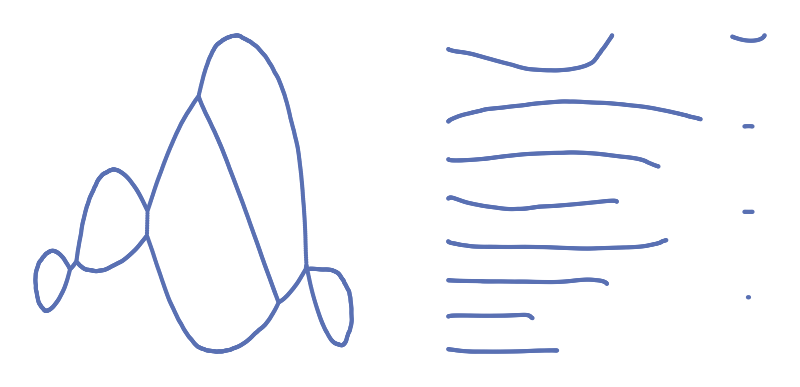

```mathematica
GraphicsRow[{loopGraphG,disconnecedLoop}={Graph[graphData],DisconnectGraph[graphData,"Graph"]}]
```

```mathematica
groupedEdges=DisconnectGraph[graphData,"Data"]
```

{{5993<->8800,5993<->8801,6000<->8801,6000<->11367,5990<->8799,5990<->8800,6003<->11366,6003<->11367,2427<->8798,2427<->8799,5991<->11340,5991<->11366,5785<->8798,5785<->11232,5992<->11339,5992<->11340,5969<->8737,5969<->11232,6001<->8733,6001<->11339,5951<->8737,5951<->11231,2371<->8711,2371<->8733,6004<->11231,6004<->11376,5941<->8711,5941<->11331,5809<->8725,5809<->11376,5934<->11300,5934<->11331,8724<->8725,8724<->8726,5944<->11300,5944<->11302,5999<->8726,5999<->11368,5886<->11301,5886<->11302,5962<->8612,5962<->11368,5936<->11301,5936<->11313,5963<->8612,5963<->8721,5901<->11291,5901<->11313,2376<->8721,2376<->8722,5943<->7043,5943<->11291,2368<->8722,2368<->8723,5902<->7043,5902<->8968,5998<->6971,5998<->8723,5940<->8719,5940<->8968,387<->6971,387<->11342,5942<->8719,5942<->8720,5985<->11342,5985<->11343,5887<->8720,5887<->11298,5964<->11343,5964<->11346,5903<->8700,5903<->11298,5967<->11346,5967<->11353,5912<->8699,5912<->8700,5979<->11353,5979<->11354,2407<->8699,2407<->11315,5957<->11354,5957<->11355,394<->8614,394<->11315,5978<->11355,5978<->11356,8613<->8614,8613<->8615,5980<->11345,5980<->11356,2359<->8615,2359<->8717,5955<->11344,5955<->11345,5898<->8717,5898<->8775,5973<->11344,5973<->11357,6990<->6991,6990<->8775,5972<->11223,5972<->11357,122<->6991,122<->8705,5781<->8730,5781<->11223,5900<->8704,5900<->8705,307<->7839,307<->8730,302<->8704,302<->8815,5977<->7839,5977<->11177,5906<->8815,5906<->8833,5960<->8589,5960<->11177,6110<->8833,6110<->8834,2373<->8588,2373<->8589,6109<->8834,6109<->11436,5971<->8588,5971<->11175,6089<->8828,6089<->11436,5956<->11162,5956<->11175,2444<->8828,2444<->11435,5665<->11162,5665<->11164,2443<->11417,2443<->11435,5664<->11163,5664<->11164,2436<->11410,2436<->11417,5655<->8532,5655<->11163,11408<->11409,11408<->11410,2413<->8315,2413<->8532,2446<->8768,2446<->11409,53<->8768,53<->8830,8829<->8830,8829<->8831,700<->7356,700<->8831,6111<->7356,6111<->11439,11438<->11439,11438<->11441,11440<->11441,11440<->11442,6114<->8637,6114<->11442,6113<->8637,6113<->11437,6122<->11437,6122<->11456,6123<->8835,6123<->11456,6115<->6964,6115<->8835,379<->6963,379<->6964,6118<->6963,6118<->11452,2524<->8960,2524<->11452,6120<->8823,6120<->8960,6084<->8822,6084<->8823,2442<->8820,2442<->8822,6302<->8805,6302<->8820,6303<->8804,6303<->8805,2434<->8804,2434<->8931,6112<->8931,6112<->11411,6274<->11411,6274<->11597,6298<->8827,6298<->11597,6297<->8826,6297<->8827,6296<->8825,6296<->8826,8824<->8825,8824<->11444,11443<->11444,11443<->11458,2499<->11455,2499<->11458,6301<->11455,6301<->11606,6299<->8959,6299<->11606,6300<->8959,6300<->11605,6276<->11600,6276<->11605,11599<->11600,11599<->11601,6282<->11577,6282<->11601,6251<->8933,6251<->11577,6277<->8932,6277<->8933,404<->8932,404<->8984,6278<->8982,6278<->8984,2430<->8840,2430<->8982,2509<->8840,2509<->8918,2535<->8918,2535<->8985,6280<->8985,6280<->8987,6279<->8987,6279<->11617,11616<->11617,11616<->11619,11618<->11619,11618<->11621,11620<->11621,11620<->11622,9678<->9680,9678<->11622,9679<->9680,9679<->9682,9681<->9682,9681<->9683,6386<->8922,6386<->9683,6321<->8922,6321<->8923,6322<->8923,6322<->11615,6393<->8878,6393<->11615,6391<->8878,6391<->8943,6390<->8935,6390<->8943},{6056<->8750,6056<->8751,6057<->8750,6057<->11396,2271<->8751,2271<->8790,6061<->11396,6061<->11397,1966<->7375,1966<->8790,6060<->8592,6060<->11397,708<->7374,708<->7375,6063<->8592,6063<->8593,6051<->7374,6051<->8776,2397<->8476,2397<->8593,2396<->8776,2396<->11389,6064<->8476,6064<->8736,374<->11389,374<->11391,2422<->8736,2422<->11398,8649<->8650,8649<->11391,5938<->8360,5938<->11398,6054<->8650,6054<->11387,2418<->8360,2418<->11381,6038<->11387,6038<->11388,6062<->11375,6062<->11381,6037<->11388,6037<->11390,5987<->11374,5987<->11375,2342<->8666,2342<->11390,6065<->11373,6065<->11374,6041<->8666,6041<->8667,6035<->11372,6035<->11373,5884<->8667,5884<->8696,6059<->11372,6059<->11395,6036<->8695,6036<->8696,6072<->11021,6072<->11395,344<->6946,344<->8695,6071<->11021,6071<->11358,6044<->6945,6044<->6946,6069<->11358,6069<->11399,6039<->6945,6039<->8681,6070<->11363,6070<->11399,6043<->8680,6043<->8681,11361<->11362,11361<->11363,6040<->8680,6040<->8682,5652<->11160,5652<->11362,6034<->8682,6034<->11314,11159<->11160,11159<->11161,6042<->11290,6042<->11314,6011<->11161,6011<->11189,6033<->11289,6033<->11290,6067<->11181,6067<->11189,5905<->11285,5905<->11289,2424<->8794,2424<->11181,5885<->8645,5885<->11285,2425<->8794,2425<->8795,6088<->8644,6088<->8645,5281<->8795,5281<->8796,441<->8644,441<->8665,6068<->8796,6068<->10945,6325<->8665,6325<->11297,5682<->8308,5682<->10945,6342<->8662,6342<->11297,5677<->8308,5677<->8793,6344<->6987,6344<->8662,5287<->8793,5287<->10943,386<->6987,386<->8718,5678<->10943,5678<->10944,2352<->8698,2352<->8718,5684<->10944,5684<->11188,8697<->8698,8697<->11637,5644<->8324,5644<->11188,6324<->11286,6324<->11637,2023<->8324,2023<->8362,6327<->11247,6327<->11286,5292<->8362,5292<->8363,11246<->11247,11246<->11248,5286<->8363,5286<->8372,6337<->11248,6337<->11249,1973<->8325,1973<->8372,6338<->11249,6338<->11629,1980<->8325,1980<->8326,6329<->11284,6329<->11629,5290<->8326,5290<->8331,6339<->11284,6339<->11631,5293<->8331,5293<->10966,6328<->11250,6328<->11631,5311<->10952,5311<->10966,5815<->8955,5815<->11250,5297<->8371,5297<->10952,6326<->8955,6326<->11630,8369<->8370,8369<->8371,6330<->11628,6330<->11630,5288<->8370,5288<->10965,6382<->11627,6382<->11628,10963<->10964,10963<->10965,6381<->11252,6381<->11627,10961<->10962,10961<->10964,6331<->11251,6331<->11252,5303<->10953,5303<->10962,6380<->8693,6380<->11251,5298<->10953,5298<->10973,8692<->8693,8692<->8694,5285<->10958,5285<->10973,6404<->8694,6404<->9000,5309<->10958,5309<->10959,1981<->8332,1981<->10959,5314<->8332,5314<->10957,5301<->10956,5301<->10957,5300<->10954,5300<->10956,5310<->10824,5310<->10954,5044<->8387,5044<->10824,2063<->8387,2063<->8514,5295<->8514,5295<->10951,5304<->10951,5304<->10955,5299<->8537,5299<->10955,5308<->8537},{3302<->9667,3302<->9704,3303<->9704,3303<->9706,3305<->9667,3305<->9705,3322<->9706,3322<->9725,3323<->9705,3323<->9726,6320<->8894,6320<->9725,3327<->9726,3327<->9727,8892<->8893,8892<->8894,3326<->9710,3326<->9727,2495<->8890,2495<->8893,3321<->9709,3321<->9710,3307<->9709,3307<->9711,3299<->9689,3299<->9711,3298<->9688,3298<->9689,3295<->9677,3295<->9688,3290<->9677,3290<->9698,3300<->9698,3300<->9707,3320<->9663,3320<->9707,3328<->9663,3328<->9735,3297<->9733,3297<->9735,3329<->9733,3329<->9734,3463<->9734,3463<->9847,714<->9846,714<->9847,77<->9718,77<->9846,3461<->8673,3461<->9718,716<->8673,716<->9696,715<->9696,715<->9723,7381<->7382,7381<->9723,3452<->7382,3452<->7393,3483<->7393,3483<->7400,316<->7397,316<->7400,705<->7397,705<->7398,3499<->7398,3499<->9883,3494<->9844,3494<->9883,742<->9829,742<->9844,3480<->7385,3480<->9829,717<->7385,717<->7396,3482<->7396,3482<->7401,33<->7401,33<->9841,3481<->9841,3481<->9863,3476<->9863,3476<->9864,3454<->9819,3454<->9864,3439<->9819,3439<->9828,3478<->9827,3478<->9828,9825<->9826,9825<->9827,3443<->9824,3443<->9826,3444<->8712,3444<->9824,3438<->8712,3438<->9816,3441<->9816,3441<->9818,3440<->9818,3440<->9821,3442<->9817,3442<->9821,3467<->9817,3467<->11335,5890<->11333,5890<->11335,5935<->11333,5935<->11334,5933<->9836,5933<->11334,3451<->9832,3451<->9836,5895<->7377,5895<->9832,7376<->7377,7376<->7378,5916<->7378,5916<->11308,3447<->9830,3447<->11308,5927<->9830,5927<->9831,5923<->9831,5923<->11326,5928<->11326,5928<->11327,5929<->11327,5929<->11328,5926<->8708,5926<->11328,3448<->8708,3448<->9833,5918<->9833,5918<->11309,5899<->11309,5899<->11312,5917<->6982,5917<->11312,402<->6982,402<->9809,3428<->8709,3428<->9809,5909<->8709,5909<->11429,6097<->11325,6097<->11429,3336<->11324,3336<->11325,5919<->11324,5919<->11430,2440<->8706,2440<->11430,2355<->8706,2355<->8816,6104<->8816,6104<->8817,5914<->8817,5914<->11323,6103<->11322,6103<->11323,6107<->11311,6107<->11322,6099<->9808,6099<->11311,5915<->9808,5915<->11427,6096<->6993,6096<->11427,2349<->6992,2349<->6993,407<->6992,407<->8954,6091<->8954,6091<->11419,6095<->11419,6095<->11424,11423<->11424,11423<->11425,5892<->11425,5892<->11426,6090<->8946,6090<->11426,6094<->8946,6094<->11418,6335<->11418,6335<->11636,6336<->7017,6336<->11636,2520<->7017,2520<->8949,8948<->8949,8948<->8951,8950<->8951,8950<->8952,6308<->8952,6308<->11611,6309<->11610,6309<->11611,6310<->9744,6310<->11610,6317<->9743,6317<->9744,9741<->9742,9741<->9743,6311<->9739,6311<->9742,3335<->9739,3335<->9740,826<->7486,826<->9740,6307<->7486,6307<->7488,7487<->7488},{5851<->8753,5851<->11279,5866<->8636,5866<->8753,5867<->8651,5867<->11279,5857<->8635,5857<->8636,2327<->6689,2327<->8651,2313<->8594,2313<->8635,5865<->6688,5865<->6689,5860<->8594,5860<->11287,5787<->6688,5787<->8663,5861<->11287,5861<->11288,2339<->8663,2339<->11229,5862<->8632,5862<->11288,5864<->11228,5864<->11229,5863<->8631,5863<->8632,5882<->11228,5882<->11230,2311<->8631,2311<->8671,2317<->8641,2317<->11230,378<->8671,378<->11275,5879<->8641,5879<->8690,8608<->11274,8608<->11275,5883<->8689,5883<->8690,2305<->11274,2305<->11276,2351<->8689,2351<->8691,5846<->8627,5846<->11276,5881<->8607,5881<->8691,5834<->8626,5834<->8627,5786<->8607,5786<->11233,2310<->8626,2310<->9136,5880<->6958,5880<->11233,5818<->9136,5818<->11266,2138<->6958,2138<->8463,5835<->8969,5835<->11266,5782<->8463,5782<->8652,5853<->8936,5853<->8969,2360<->8652,2360<->11377,2518<->8936,2518<->8944,6002<->11377,6002<->11378,5814<->8944,5814<->8945,6005<->11378,6005<->11379,6356<->8945,6356<->8966,2380<->8744,2380<->11379,2528<->8965,2528<->8966,6006<->8734,6006<->8744,6597<->8965,6597<->11832,6007<->8734,6007<->11352,6600<->11832,6600<->11837,5994<->11351,5994<->11352,11835<->11836,11835<->11837,2375<->11351,2375<->11371,6602<->11834,6602<->11836,5995<->11336,5995<->11371,6601<->11661,6601<->11834,5997<->8735,5997<->11336,6603<->11661,6603<->11720,2372<->6954,2372<->8735,6604<->11719,6604<->11720,5996<->6954,5996<->11369,6434<->11709,6434<->11719,5966<->11224,5966<->11369,6439<->9010,6439<->11709,2423<->8791,2423<->11224,9008<->9009,9008<->9010,5982<->8791,5982<->8792,8604<->9009,8604<->9030,5970<->8792,5970<->11364,9029<->9030,9029<->9032,5981<->11364,5981<->11365,9031<->9032,9031<->9033,5965<->8732,5965<->11365,8988<->9033,8988<->11712,2386<->7459,2386<->8732,11710<->11711,11710<->11712,2394<->7459,2394<->11359,11699<->11700,11699<->11711,5667<->11185,5667<->11359,11697<->11698,11697<->11700,5976<->8797,5976<->11185,11245<->11694,11245<->11698,5975<->8727,5975<->8797,11693<->11694,11693<->11695,5779<->6938,5779<->8727,6431<->11695,6431<->11696,342<->6938,342<->6939,6432<->9001,6432<->11696,5968<->6939,5968<->6940,5974<->6940,5974<->6941,5656<->6941,5656<->8590,2275<->7854,2275<->8590,2367<->7854,2367<->8533,2370<->8533,2370<->11165,5375<->8395,5375<->11165},{133<->6778,133<->10271,4919<->6778,4919<->8220,10270<->10271,10270<->10272,4916<->8073,4916<->8220,1268<->10247,1268<->10272,4917<->8072,4917<->8073,4937<->10247,4937<->10248,1671<->6809,1671<->8072,4936<->10248,4936<->10249,4918<->6809,4918<->10756,4930<->10249,4930<->10774,10755<->10756,10755<->10757,201<->10774,201<->10776,1686<->10268,1686<->10757,4939<->10775,4939<->10776,4116<->10268,4116<->10269,4938<->8071,4938<->10775,4902<->10269,4902<->10743,4999<->8070,4999<->8071,4945<->10743,4945<->10744,5000<->8070,5000<->8127,4942<->10744,4942<->10778,1713<->8126,1713<->8127,4940<->8095,4940<->10778,5002<->8126,5002<->10803,4941<->8095,4941<->8101,4998<->7620,4998<->10803,4101<->8101,4101<->10250,989<->7620,989<->7621,1692<->8103,1692<->10250,5004<->7621,5004<->10804,8102<->8103,8102<->8104,5010<->6826,5010<->10804,1693<->8104,1693<->10738,5001<->6826,5001<->8133,4944<->8089,4944<->10738,1695<->8106,1695<->8133,4893<->6885,4893<->8089,4929<->8106,4929<->10766,4943<->6885,4943<->8081,5009<->10766,5009<->10767,270<->8081,270<->10736,5011<->10767,5011<->10768,4921<->10735,4921<->10736,1712<->10768,1712<->10769,10734<->10735,10734<->10737,4994<->8123,4994<->10769,4894<->10737,4894<->10739,4895<->8099,4895<->10739,8097<->8098,8097<->8099,4891<->7619,4891<->8098,4889<->7619,4889<->10747,4884<->10747,4884<->10748,4915<->10748,4915<->10754,4880<->10752,4880<->10754,4920<->10730,4920<->10752,4908<->8045,4908<->10730,1639<->8045,1639<->10751,4947<->8085,4947<->10751,4923<->8084,4923<->8085,1670<->8084,1670<->10762,4946<->10759,4946<->10762,4922<->10758,4922<->10759,1672<->8060,1672<->10758,1649<->7583,1649<->8060,932<->7582,932<->7583,4933<->7582,4933<->8054,1647<->6785,1647<->8054,152<->6785,152<->6829,4932<->6829,4932<->8105,4038<->8105,4038<->10204,4090<->6864,4090<->10204,4048<->6864,4048<->7896,4924<->7896,4924<->8128,4934<->8128,4934<->10770,1599<->10196,1599<->10770,5005<->10196,5005<->10805,1701<->8107,1701<->10805,4996<->8107,4996<->10771,1674<->8080,1674<->10771,5003<->8080,5003<->10772,1667<->10772,1667<->10806,5007<->10806,5007<->10807,5006<->10798,5006<->10807,4989<->10777,4989<->10798,4983<->8129,4983<->10777},{5019<->10239,5019<->10240,4084<->10239,4084<->10788,4979<->7872,4979<->10240,1728<->8183,1728<->10788,5022<->7872,5022<->8385,2066<->8183,2066<->8184,5021<->8341,5021<->8385,4956<->8184,4956<->10781,5020<->8341,5020<->8391,4964<->10781,4964<->10782,1997<->6918,1997<->8391,1719<->8139,1719<->10782,2065<->6917,2065<->6918,1984<->8139,1984<->8140,5338<->6915,5338<->6917,1004<->7635,1004<->8140,5018<->6915,5018<->6916,4965<->7634,4965<->7635,5389<->6916,5389<->11025,4958<->7634,4958<->8110,5393<->8179,5393<->11025,4963<->8110,4963<->8111,5397<->8178,5397<->8179,4072<->8111,4072<->10232,5392<->8177,5392<->8178,1694<->6673,1694<->10232,1754<->8176,1754<->8177,6671<->6672,6671<->6673,2067<->8176,2067<->8558,4967<->6665,4967<->6672,2070<->8555,2070<->8558,18<->6665,18<->6666,5028<->8555,5028<->10816,4970<->6666,4970<->6667,5379<->10816,5379<->11024,1710<->6667,1710<->8121,5399<->8556,5399<->11024,4953<->8118,4953<->8121,5400<->8556,5400<->11026,8116<->8117,8116<->8118,5394<->10980,5394<->11026,4976<->8117,4976<->10629,1994<->10980,1994<->10981,4977<->8092,4977<->10629,5395<->8389,5395<->10981,4968<->8092,4968<->10790,5396<->8345,5396<->8389,4973<->10243,4973<->10790,5398<->8344,5398<->8345,4961<->10243,4961<->10783,1999<->8344,1999<->10997,4972<->10780,4972<->10783,5388<->10988,5388<->10997,4950<->10780,4950<->10784,5335<->10987,5335<->10988,4794<->10686,4794<->10784,5327<->10987,5327<->10996,4978<->10686,4978<->10687,10994<->10995,10994<->10996,4959<->10687,4959<->10688,10992<->10993,10992<->10995,4971<->10688,4971<->10689,5331<->10990,5331<->10993,4833<->10689,4833<->10690,5324<->10990,5324<->10991,4975<->10690,4975<->10791,5317<->8340,5317<->10991,1783<->10218,1783<->10791,5325<->8340,5325<->10998,4980<->10218,4980<->10795,5334<->10998,5334<->10999,4993<->10792,4993<->10795,5332<->10982,5332<->10999,4974<->10792,4974<->10793,5333<->10971,5333<->10982,4995<->10793,4995<->10794,5342<->10971,5342<->11000,4949<->8130,4949<->10794,4827<->8130,4827<->8158,4992<->8113,4992<->8158},{5030<->8189,5030<->8191,1766<->8147,1766<->8189,4962<->8191,4962<->10809,1727<->8147,1727<->10810,5034<->10809,5034<->10811,5032<->10786,5032<->10810,5039<->10796,5039<->10811,2064<->8390,2064<->10786,5036<->10796,5036<->10817,5024<->8192,5024<->8390,5037<->8143,5037<->10817,5025<->7826,5025<->8192,5023<->8143,5023<->8144,1265<->7826,1265<->7863,5031<->8144,5031<->10813,5029<->7863,5029<->7864,1724<->8119,1724<->10813,5027<->7864,5027<->8174,1700<->7636,1700<->8119,4553<->8173,4553<->8174,1005<->7636,1005<->8137,5390<->8173,5390<->10815,4955<->8137,4955<->8141,5391<->10814,5391<->10815,4951<->8141,4951<->8142,5321<->6900,5321<->10814,4952<->8142,4952<->10819,298<->6900,298<->6901,5038<->10224,5038<->10819,5322<->6901,5322<->8392,5016<->10224,5016<->10797,1342<->8193,1342<->8392,1698<->6876,1698<->10797,1976<->8186,1976<->8193,1717<->6875,1717<->6876,1760<->8186,1760<->10984,259<->6875,259<->6877,1988<->8337,1988<->10984,4986<->6877,4986<->8078,2058<->8327,2058<->8337,1702<->8077,1702<->8078,5320<->8171,5320<->8327,1673<->8077,1673<->8079,273<->8171,273<->8393,4987<->8079,4987<->10799,1749<->8393,1749<->8394,4985<->10219,4985<->10799,5336<->8138,5336<->8394,4981<->8154,4981<->10219,2061<->8114,2061<->8138,1715<->8131,1715<->8154,1990<->8114,1990<->8339,5330<->8339,5330<->10969,5337<->8109,5337<->10969,1697<->8109},{1972<->8540,1972<->8541,5692<->8538,5692<->8540,5316<->8541,5316<->10977,2235<->8538,2235<->8539,2208<->10972,2208<->10977,5693<->8539,5693<->11193,5312<->8346,5312<->10972,5694<->10960,5694<->11193,5339<->8346,5339<->8347,5315<->8115,5315<->10960,5344<->8347,5344<->11001,2225<->8115,2225<->10974,5326<->10985,5326<->11001,5345<->9977,5345<->10974,5346<->10985,5346<->10986,5696<->8317,5696<->9977,2232<->10975,2232<->10986,5689<->8317,5689<->11195,5313<->8323,5313<->10975,5699<->8375,5699<->11195,5328<->8322,5328<->8323,2228<->8375,2228<->8542,5698<->8542,5698<->8543,5662<->8543,5662<->10976,5700<->9978,5700<->10976,5701<->7366,5701<->9978,5680<->7364,5680<->7366,2227<->7364,2227<->7365,5660<->7365,5660<->11178,5688<->11178,5688<->11179,5686<->11167,5686<->11179,5679<->11167,5679<->11169,11168<->11169,11168<->11171,11170<->11171,11170<->11172,5663<->11172,5663<->11182,787<->7451,787<->11182,5672<->7451,5672<->7452,5671<->7452,5671<->8529,5653<->6907,5653<->8529,5666<->6907,5666<->11183,5669<->11183,5669<->11184,5670<->8504,5670<->11184,2192<->8314,2192<->8504},{6421<->9664,6421<->11708,6423<->9664,6423<->9665,6419<->11675,6419<->11708,6422<->8940,6422<->9665,6420<->11675,6420<->11676,6394<->8940,6394<->11257,6418<->7304,6418<->11676,6385<->11257,6385<->11258,6379<->7304,6379<->9692,6384<->9003,6384<->11258,9690<->9691,9690<->9692,6397<->9002,6397<->9003,8813<->8814,8813<->9691,8811<->8812,8811<->8814,6332<->8812,6332<->9729,9728<->9729,9728<->9730,7490<->7491,7490<->9730,7489<->7491},{1664<->8134,1664<->10779,1711<->8112,1711<->8134,4954<->8125,4954<->10779,4948<->8124,4948<->8125},{2000<->9974,2000<->9975,5329<->9975,5329<->9976,1720<->1993,1720<->9976,1993<->8388,5341<->8388},{7492<->8934}}

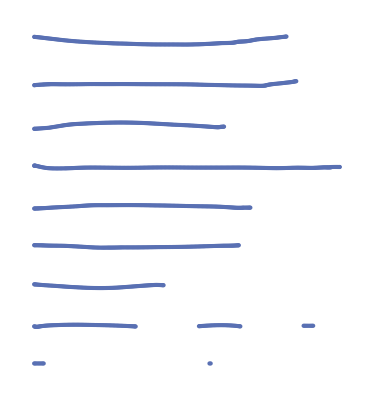

```mathematica
Graph[Flatten@groupedEdges]
```

```mathematica
resDeleteEdge11=DeleteEdge[graphData,groupedEdges⟦11⟧]
```

{18<->6665,18<->6666,33<->7401,33<->9841,53<->8768,53<->8830,77<->9718,77<->9846,122<->6991,122<->8705,133<->6778,133<->10271,152<->6785,152<->6829,201<->10774,201<->10776,259<->6875,259<->6877,270<->8081,270<->10736,273<->8171,273<->8393,298<->6900,298<->6901,302<->8704,302<->8815,307<->7839,307<->8730,316<->7397,316<->7400,342<->6938,342<->6939,344<->6946,344<->8695,374<->11389,374<->11391,378<->8671,378<->11275,379<->6963,379<->6964,386<->6987,386<->8718,387<->6971,387<->11342,394<->8614,394<->11315,402<->6982,402<->9809,404<->8932,404<->8984,407<->6992,407<->8954,441<->8644,441<->8665,700<->7356,700<->8831,705<->7397,705<->7398,708<->7374,708<->7375,714<->9846,714<->9847,715<->9696,715<->9723,716<->8673,716<->9696,717<->7385,717<->7396,742<->9829,742<->9844,787<->7451,787<->11182,826<->7486,826<->9740,932<->7582,932<->7583,989<->7620,989<->7621,1004<->7635,1004<->8140,1005<->7636,1005<->8137,1265<->7826,1265<->7863,1268<->10247,1268<->10272,1342<->8193,1342<->8392,1599<->10196,1599<->10770,1639<->8045,1639<->10751,1647<->6785,1647<->8054,1649<->7583,1649<->8060,1664<->8134,1664<->10779,1667<->10772,1667<->10806,1670<->8084,1670<->10762,1671<->6809,1671<->8072,1672<->8060,1672<->10758,1673<->8077,1673<->8079,1674<->8080,1674<->10771,1686<->10268,1686<->10757,1692<->8103,1692<->10250,1693<->8104,1693<->10738,1694<->6673,1694<->10232,1695<->8106,1695<->8133,1697<->8108,1697<->8109,1698<->6876,1698<->10797,1700<->7636,1700<->8119,1701<->8107,1701<->10805,1702<->8077,1702<->8078,1710<->6667,1710<->8121,1711<->8112,1711<->8134,1712<->10768,1712<->10769,1713<->8126,1713<->8127,1715<->8131,1715<->8154,1717<->6875,1717<->6876,1719<->8139,1719<->10782,1724<->8119,1724<->10813,1727<->8147,1727<->10810,1728<->8183,1728<->10788,1749<->8393,1749<->8394,1754<->8176,1754<->8177,1760<->8186,1760<->10984,1766<->8147,1766<->8189,1783<->10218,1783<->10791,1966<->7375,1966<->8790,1972<->8540,1972<->8541,1973<->8325,1973<->8372,1976<->8186,1976<->8193,1980<->8325,1980<->8326,1981<->8332,1981<->10959,1984<->8139,1984<->8140,1988<->8337,1988<->10984,1990<->8114,1990<->8339,1994<->10980,1994<->10981,1997<->6918,1997<->8391,1999<->8344,1999<->10997,2023<->8324,2023<->8362,2058<->8327,2058<->8337,2061<->8114,2061<->8138,2063<->8387,2063<->8514,2064<->8390,2064<->10786,2065<->6917,2065<->6918,2066<->8183,2066<->8184,2067<->8176,2067<->8558,2068<->8314,2068<->8315,2068<->8395,2070<->8555,2070<->8558,2138<->6958,2138<->8463,2192<->8314,2192<->8504,2208<->10972,2208<->10977,2225<->8115,2225<->10974,2227<->7364,2227<->7365,2228<->8375,2228<->8542,2232<->10975,2232<->10986,2235<->8538,2235<->8539,2271<->8751,2271<->8790,2275<->7854,2275<->8590,2305<->11274,2305<->11276,2310<->8626,2310<->9136,2311<->8631,2311<->8671,2313<->8594,2313<->8635,2317<->8641,2317<->11230,2327<->6689,2327<->8651,2339<->8663,2339<->11229,2342<->8666,2342<->11390,2349<->6992,2349<->6993,2351<->8689,2351<->8691,2352<->8698,2352<->8718,2355<->8706,2355<->8816,2359<->8615,2359<->8717,2360<->8652,2360<->11377,2367<->7854,2367<->8533,2368<->8722,2368<->8723,2370<->8533,2370<->11165,2371<->8711,2371<->8733,2372<->6954,2372<->8735,2373<->8588,2373<->8589,2375<->11351,2375<->11371,2376<->8721,2376<->8722,2380<->8744,2380<->11379,2386<->7459,2386<->8732,2394<->7459,2394<->11359,2396<->8776,2396<->11389,2397<->8476,2397<->8593,2407<->8699,2407<->11315,2413<->8315,2413<->8532,2418<->8360,2418<->11381,2422<->8736,2422<->11398,2423<->8791,2423<->11224,2424<->8794,2424<->11181,2425<->8794,2425<->8795,2427<->8798,2427<->8799,2430<->8840,2430<->8982,2434<->8804,2434<->8931,2436<->11410,2436<->11417,2440<->8706,2440<->11430,2442<->8820,2442<->8822,2443<->11417,2443<->11435,2444<->8828,2444<->11435,2446<->8768,2446<->11409,2495<->8890,2495<->8893,2499<->11455,2499<->11458,2509<->8840,2509<->8918,2518<->8936,2518<->8944,2520<->7017,2520<->8949,2524<->8960,2524<->11452,2528<->8965,2528<->8966,2535<->8918,2535<->8985,3290<->9677,3290<->9698,3295<->9677,3295<->9688,3297<->9733,3297<->9735,3298<->9688,3298<->9689,3299<->9689,3299<->9711,3300<->9698,3300<->9707,3302<->9667,3302<->9704,3303<->9704,3303<->9706,3305<->9667,3305<->9705,3307<->9709,3307<->9711,3320<->9663,3320<->9707,3321<->9709,3321<->9710,3322<->9706,3322<->9725,3323<->9705,3323<->9726,3326<->9710,3326<->9727,3327<->9726,3327<->9727,3328<->9663,3328<->9735,3329<->9733,3329<->9734,3335<->9739,3335<->9740,3336<->11324,3336<->11325,3428<->8709,3428<->9809,3438<->8712,3438<->9816,3439<->9819,3439<->9828,3440<->9818,3440<->9821,3441<->9816,3441<->9818,3442<->9817,3442<->9821,3443<->9824,3443<->9826,3444<->8712,3444<->9824,3447<->9830,3447<->11308,3448<->8708,3448<->9833,3451<->9832,3451<->9836,3452<->7382,3452<->7393,3454<->9819,3454<->9864,3461<->8673,3461<->9718,3463<->9734,3463<->9847,3467<->9817,3467<->11335,3476<->9863,3476<->9864,3478<->9827,3478<->9828,3480<->7385,3480<->9829,3481<->9841,3481<->9863,3482<->7396,3482<->7401,3483<->7393,3483<->7400,3494<->9844,3494<->9883,3499<->7398,3499<->9883,4038<->8105,4038<->10204,4048<->6864,4048<->7896,4072<->8111,4072<->10232,4084<->10239,4084<->10788,4090<->6864,4090<->10204,4101<->8101,4101<->10250,4116<->10268,4116<->10269,4553<->8173,4553<->8174,4794<->10686,4794<->10784,4827<->8130,4827<->8158,4833<->10689,4833<->10690,4880<->10752,4880<->10754,4884<->10747,4884<->10748,4889<->7619,4889<->10747,4891<->7619,4891<->8098,4893<->6885,4893<->8089,4894<->10737,4894<->10739,4895<->8099,4895<->10739,4902<->10269,4902<->10743,4908<->8045,4908<->10730,4915<->10748,4915<->10754,4916<->8073,4916<->8220,4917<->8072,4917<->8073,4918<->6809,4918<->10756,4919<->6778,4919<->8220,4920<->10730,4920<->10752,4921<->10735,4921<->10736,4922<->10758,4922<->10759,4923<->8084,4923<->8085,4924<->7896,4924<->8128,4929<->8106,4929<->10766,4930<->10249,4930<->10774,4932<->6829,4932<->8105,4933<->7582,4933<->8054,4934<->8128,4934<->10770,4936<->10248,4936<->10249,4937<->10247,4937<->10248,4938<->8071,4938<->10775,4939<->10775,4939<->10776,4940<->8095,4940<->10778,4941<->8095,4941<->8101,4942<->10744,4942<->10778,4943<->6885,4943<->8081,4944<->8089,4944<->10738,4945<->10743,4945<->10744,4946<->10759,4946<->10762,4947<->8085,4947<->10751,4948<->8124,4948<->8125,4949<->8130,4949<->10794,4950<->10780,4950<->10784,4951<->8141,4951<->8142,4952<->8142,4952<->10819,4953<->8118,4953<->8121,4954<->8125,4954<->10779,4955<->8137,4955<->8141,4956<->8184,4956<->10781,4958<->7634,4958<->8110,4959<->10687,4959<->10688,4961<->10243,4961<->10783,4962<->8191,4962<->10809,4963<->8110,4963<->8111,4964<->10781,4964<->10782,4965<->7634,4965<->7635,4967<->6665,4967<->6672,4968<->8092,4968<->10790,4970<->6666,4970<->6667,4971<->10688,4971<->10689,4972<->10780,4972<->10783,4973<->10243,4973<->10790,4974<->10792,4974<->10793,4975<->10690,4975<->10791,4976<->8117,4976<->10629,4977<->8092,4977<->10629,4978<->10686,4978<->10687,4979<->7872,4979<->10240,4980<->10218,4980<->10795,4981<->8154,4981<->10219,4983<->8129,4983<->10777,4984<->8112,4984<->8113,4984<->8131,4985<->10219,4985<->10799,4986<->6877,4986<->8078,4987<->8079,4987<->10799,4989<->10777,4989<->10798,4991<->8123,4991<->8124,4991<->8129,4992<->8113,4992<->8158,4993<->10792,4993<->10795,4994<->8123,4994<->10769,4995<->10793,4995<->10794,4996<->8107,4996<->10771,4998<->7620,4998<->10803,4999<->8070,4999<->8071,5000<->8070,5000<->8127,5001<->6826,5001<->8133,5002<->8126,5002<->10803,5003<->8080,5003<->10772,5004<->7621,5004<->10804,5005<->10196,5005<->10805,5006<->10798,5006<->10807,5007<->10806,5007<->10807,5009<->10766,5009<->10767,5010<->6826,5010<->10804,5011<->10767,5011<->10768,5016<->10224,5016<->10797,5018<->6915,5018<->6916,5019<->10239,5019<->10240,5020<->8341,5020<->8391,5021<->8341,5021<->8385,5022<->7872,5022<->8385,5023<->8143,5023<->8144,5024<->8192,5024<->8390,5025<->7826,5025<->8192,5027<->7864,5027<->8174,5028<->8555,5028<->10816,5029<->7863,5029<->7864,5030<->8189,5030<->8191,5031<->8144,5031<->10813,5032<->10786,5032<->10810,5034<->10809,5034<->10811,5036<->10796,5036<->10817,5037<->8143,5037<->10817,5038<->10224,5038<->10819,5039<->10796,5039<->10811,5044<->8387,5044<->10824,5281<->8795,5281<->8796,5285<->10958,5285<->10973,5286<->8363,5286<->8372,5287<->8793,5287<->10943,5288<->8370,5288<->10965,5290<->8326,5290<->8331,5292<->8362,5292<->8363,5293<->8331,5293<->10966,5295<->8514,5295<->10951,5297<->8371,5297<->10952,5298<->10953,5298<->10973,5299<->8537,5299<->10955,5300<->10954,5300<->10956,5301<->10956,5301<->10957,5303<->10953,5303<->10962,5304<->10951,5304<->10955,5308<->8108,5308<->8537,5309<->10958,5309<->10959,5310<->10824,5310<->10954,5311<->10952,5311<->10966,5312<->8346,5312<->10972,5313<->8323,5313<->10975,5314<->8332,5314<->10957,5315<->8115,5315<->10960,5316<->8541,5316<->10977,5317<->8340,5317<->10991,5320<->8171,5320<->8327,5321<->6900,5321<->10814,5322<->6901,5322<->8392,5324<->10990,5324<->10991,5325<->8340,5325<->10998,5326<->10985,5326<->11001,5327<->10987,5327<->10996,5328<->8322,5328<->8323,5330<->8339,5330<->10969,5331<->10990,5331<->10993,5332<->10982,5332<->10999,5333<->10971,5333<->10982,5334<->10998,5334<->10999,5335<->10987,5335<->10988,5336<->8138,5336<->8394,5337<->8109,5337<->10969,5338<->6915,5338<->6917,5339<->8346,5339<->8347,5340<->8322,5340<->9974,5340<->11000,5341<->8108,5342<->10971,5342<->11000,5344<->8347,5344<->11001,5345<->9977,5345<->10974,5346<->10985,5346<->10986,5375<->8395,5375<->11165,5379<->10816,5379<->11024,5388<->10988,5388<->10997,5389<->6916,5389<->11025,5390<->8173,5390<->10815,5391<->10814,5391<->10815,5392<->8177,5392<->8178,5393<->8179,5393<->11025,5394<->10980,5394<->11026,5395<->8389,5395<->10981,5396<->8345,5396<->8389,5397<->8178,5397<->8179,5398<->8344,5398<->8345,5399<->8556,5399<->11024,5400<->8556,5400<->11026,5644<->8324,5644<->11188,5652<->11160,5652<->11362,5653<->6907,5653<->8529,5655<->8532,5655<->11163,5656<->6941,5656<->8590,5660<->7365,5660<->11178,5662<->8543,5662<->10976,5663<->11172,5663<->11182,5664<->11163,5664<->11164,5665<->11162,5665<->11164,5666<->6907,5666<->11183,5667<->11185,5667<->11359,5669<->11183,5669<->11184,5670<->8504,5670<->11184,5671<->7452,5671<->8529,5672<->7451,5672<->7452,5677<->8308,5677<->8793,5678<->10943,5678<->10944,5679<->11167,5679<->11169,5680<->7364,5680<->7366,5682<->8308,5682<->10945,5684<->10944,5684<->11188,5686<->11167,5686<->11179,5688<->11178,5688<->11179,5689<->8317,5689<->11195,5692<->8538,5692<->8540,5693<->8539,5693<->11193,5694<->10960,5694<->11193,5696<->8317,5696<->9977,5698<->8542,5698<->8543,5699<->8375,5699<->11195,5700<->9978,5700<->10976,5701<->7366,5701<->9978,5779<->6938,5779<->8727,5781<->8730,5781<->11223,5782<->8463,5782<->8652,5785<->8798,5785<->11232,5786<->8607,5786<->11233,5787<->6688,5787<->8663,5809<->8725,5809<->11376,5814<->8944,5814<->8945,5815<->8955,5815<->11250,5818<->9136,5818<->11266,5834<->8626,5834<->8627,5835<->8969,5835<->11266,5846<->8627,5846<->11276,5851<->8753,5851<->11279,5853<->8936,5853<->8969,5857<->8635,5857<->8636,5860<->8594,5860<->11287,5861<->11287,5861<->11288,5862<->8632,5862<->11288,5863<->8631,5863<->8632,5864<->11228,5864<->11229,5865<->6688,5865<->6689,5866<->8636,5866<->8753,5867<->8651,5867<->11279,5879<->8641,5879<->8690,5880<->6958,5880<->11233,5881<->8607,5881<->8691,5882<->11228,5882<->11230,5883<->8689,5883<->8690,5884<->8667,5884<->8696,5885<->8645,5885<->11285,5886<->11301,5886<->11302,5887<->8720,5887<->11298,5890<->11333,5890<->11335,5892<->11425,5892<->11426,5895<->7377,5895<->9832,5898<->8717,5898<->8775,5899<->11309,5899<->11312,5900<->8704,5900<->8705,5901<->11291,5901<->11313,5902<->7043,5902<->8968,5903<->8700,5903<->11298,5905<->11285,5905<->11289,5906<->8815,5906<->8833,5909<->8709,5909<->11429,5912<->8699,5912<->8700,5914<->8817,5914<->11323,5915<->9808,5915<->11427,5916<->7378,5916<->11308,5917<->6982,5917<->11312,5918<->9833,5918<->11309,5919<->11324,5919<->11430,5923<->9831,5923<->11326,5926<->8708,5926<->11328,5927<->9830,5927<->9831,5928<->11326,5928<->11327,5929<->11327,5929<->11328,5933<->9836,5933<->11334,5934<->11300,5934<->11331,5935<->11333,5935<->11334,5936<->11301,5936<->11313,5938<->8360,5938<->11398,5940<->8719,5940<->8968,5941<->8711,5941<->11331,5942<->8719,5942<->8720,5943<->7043,5943<->11291,5944<->11300,5944<->11302,5951<->8737,5951<->11231,5955<->11344,5955<->11345,5956<->11162,5956<->11175,5957<->11354,5957<->11355,5960<->8589,5960<->11177,5962<->8612,5962<->11368,5963<->8612,5963<->8721,5964<->11343,5964<->11346,5965<->8732,5965<->11365,5966<->11224,5966<->11369,5967<->11346,5967<->11353,5968<->6939,5968<->6940,5969<->8737,5969<->11232,5970<->8792,5970<->11364,5971<->8588,5971<->11175,5972<->11223,5972<->11357,5973<->11344,5973<->11357,5974<->6940,5974<->6941,5975<->8727,5975<->8797,5976<->8797,5976<->11185,5977<->7839,5977<->11177,5978<->11355,5978<->11356,5979<->11353,5979<->11354,5980<->11345,5980<->11356,5981<->11364,5981<->11365,5982<->8791,5982<->8792,5985<->11342,5985<->11343,5987<->11374,5987<->11375,5990<->8799,5990<->8800,5991<->11340,5991<->11366,5992<->11339,5992<->11340,5993<->8800,5993<->8801,5994<->11351,5994<->11352,5995<->11336,5995<->11371,5996<->6954,5996<->11369,5997<->8735,5997<->11336,5998<->6971,5998<->8723,5999<->8726,5999<->11368,6000<->8801,6000<->11367,6001<->8733,6001<->11339,6002<->11377,6002<->11378,6003<->11366,6003<->11367,6004<->11231,6004<->11376,6005<->11378,6005<->11379,6006<->8734,6006<->8744,6007<->8734,6007<->11352,6011<->11161,6011<->11189,6033<->11289,6033<->11290,6034<->8682,6034<->11314,6035<->11372,6035<->11373,6036<->8695,6036<->8696,6037<->11388,6037<->11390,6038<->11387,6038<->11388,6039<->6945,6039<->8681,6040<->8680,6040<->8682,6041<->8666,6041<->8667,6042<->11290,6042<->11314,6043<->8680,6043<->8681,6044<->6945,6044<->6946,6051<->7374,6051<->8776,6054<->8650,6054<->11387,6056<->8750,6056<->8751,6057<->8750,6057<->11396,6059<->11372,6059<->11395,6060<->8592,6060<->11397,6061<->11396,6061<->11397,6062<->11375,6062<->11381,6063<->8592,6063<->8593,6064<->8476,6064<->8736,6065<->11373,6065<->11374,6067<->11181,6067<->11189,6068<->8796,6068<->10945,6069<->11358,6069<->11399,6070<->11363,6070<->11399,6071<->11021,6071<->11358,6072<->11021,6072<->11395,6084<->8822,6084<->8823,6088<->8644,6088<->8645,6089<->8828,6089<->11436,6090<->8946,6090<->11426,6091<->8954,6091<->11419,6094<->8946,6094<->11418,6095<->11419,6095<->11424,6096<->6993,6096<->11427,6097<->11325,6097<->11429,6099<->9808,6099<->11311,6103<->11322,6103<->11323,6104<->8816,6104<->8817,6107<->11311,6107<->11322,6109<->8834,6109<->11436,6110<->8833,6110<->8834,6111<->7356,6111<->11439,6112<->8931,6112<->11411,6113<->8637,6113<->11437,6114<->8637,6114<->11442,6115<->6964,6115<->8835,6118<->6963,6118<->11452,6120<->8823,6120<->8960,6122<->11437,6122<->11456,6123<->8835,6123<->11456,6251<->8933,6251<->11577,6274<->11411,6274<->11597,6276<->11600,6276<->11605,6277<->8932,6277<->8933,6278<->8982,6278<->8984,6279<->8987,6279<->11617,6280<->8985,6280<->8987,6282<->11577,6282<->11601,6296<->8825,6296<->8826,6297<->8826,6297<->8827,6298<->8827,6298<->11597,6299<->8959,6299<->11606,6300<->8959,6300<->11605,6301<->11455,6301<->11606,6302<->8805,6302<->8820,6303<->8804,6303<->8805,6307<->7486,6307<->7488,6308<->8952,6308<->11611,6309<->11610,6309<->11611,6310<->9744,6310<->11610,6311<->9739,6311<->9742,6317<->9743,6317<->9744,6320<->8894,6320<->9725,6321<->8922,6321<->8923,6322<->8923,6322<->11615,6324<->11286,6324<->11637,6325<->8665,6325<->11297,6326<->8955,6326<->11630,6327<->11247,6327<->11286,6328<->11250,6328<->11631,6329<->11284,6329<->11629,6330<->11628,6330<->11630,6331<->11251,6331<->11252,6332<->8812,6332<->9729,6335<->11418,6335<->11636,6336<->7017,6336<->11636,6337<->11248,6337<->11249,6338<->11249,6338<->11629,6339<->11284,6339<->11631,6342<->8662,6342<->11297,6344<->6987,6344<->8662,6356<->8945,6356<->8966,6379<->7304,6379<->9692,6380<->8693,6380<->11251,6381<->11252,6381<->11627,6382<->11627,6382<->11628,6384<->9003,6384<->11258,6385<->11257,6385<->11258,6386<->8922,6386<->9683,6390<->8935,6390<->8943,6391<->8878,6391<->8943,6392<->8890,6392<->8934,6392<->8935,6393<->8878,6393<->11615,6394<->8940,6394<->11257,6397<->9002,6397<->9003,6404<->8694,6404<->9000,6418<->7304,6418<->11676,6419<->11675,6419<->11708,6420<->11675,6420<->11676,6421<->9664,6421<->11708,6422<->8940,6422<->9665,6423<->9664,6423<->9665,6431<->11695,6431<->11696,6432<->9001,6432<->11696,6434<->11709,6434<->11719,6439<->9010,6439<->11709,6441<->9000,6441<->9001,6441<->9002,6597<->8965,6597<->11832,6600<->11832,6600<->11837,6601<->11661,6601<->11834,6602<->11834,6602<->11836,6603<->11661,6603<->11720,6604<->11719,6604<->11720,6671<->6672,6671<->6673,6990<->6991,6990<->8775,7376<->7377,7376<->7378,7381<->7382,7381<->9723,7487<->7488,7487<->7493,7489<->7491,7489<->7493,7490<->7491,7490<->9730,7492<->7493,7492<->8934,8097<->8098,8097<->8099,8102<->8103,8102<->8104,8116<->8117,8116<->8118,8369<->8370,8369<->8371,8604<->9009,8604<->9030,8608<->11274,8608<->11275,8613<->8614,8613<->8615,8649<->8650,8649<->11391,8692<->8693,8692<->8694,8697<->8698,8697<->11637,8724<->8725,8724<->8726,8811<->8812,8811<->8814,8813<->8814,8813<->9691,8824<->8825,8824<->11444,8829<->8830,8829<->8831,8892<->8893,8892<->8894,8948<->8949,8948<->8951,8950<->8951,8950<->8952,8988<->9033,8988<->11712,9008<->9009,9008<->9010,9029<->9030,9029<->9032,9031<->9032,9031<->9033,9678<->9680,9678<->11622,9679<->9680,9679<->9682,9681<->9682,9681<->9683,9690<->9691,9690<->9692,9728<->9729,9728<->9730,9741<->9742,9741<->9743,9825<->9826,9825<->9827,10270<->10271,10270<->10272,10734<->10735,10734<->10737,10755<->10756,10755<->10757,10961<->10962,10961<->10964,10963<->10964,10963<->10965,10992<->10993,10992<->10995,10994<->10995,10994<->10996,11159<->11160,11159<->11161,11168<->11169,11168<->11171,11170<->11171,11170<->11172,11245<->11694,11245<->11698,11246<->11247,11246<->11248,11361<->11362,11361<->11363,11408<->11409,11408<->11410,11423<->11424,11423<->11425,11438<->11439,11438<->11441,11440<->11441,11440<->11442,11443<->11444,11443<->11458,11599<->11600,11599<->11601,11616<->11617,11616<->11619,11618<->11619,11618<->11621,11620<->11621,11620<->11622,11693<->11694,11693<->11695,11697<->11698,11697<->11700,11699<->11700,11699<->11711,11710<->11711,11710<->11712,11835<->11836,11835<->11837}

```mathematica
VisualizeRootGraphics3D[vertices, GraphConvert@resDeleteEdge11, Red]
```

-Graphics3D-